# 3.3 : Lyapunov exponents for the Lorenz model

#### a)

Initialise parameters

```mathematica
σ = 10;
b = 8/3;
r = 28;
```

```mathematica
ts = 1; (* we start at a later time to get rid of the initial transient *)
```

```mathematica
dt = 10^-4;
```

```mathematica
n = 10^6;
```

```mathematica
T = n*dt+ts
```

101

```mathematica
sol2[x0_ , y0_,z0_] :=NDSolve[
{x'[t]== σ*(y[t]-x[t]), 
y'[t] == r*x[t]-y[t]-x[t]*z[t], z'[t] ==x[t]*y[t]-b*z[t] , x[0] == x0 , y[0] == y0,z[0]==z0} 
, {x,y,z} ,{t,ts,T}, StartingStepSize->dt, Method->"ExplicitRungeKutta", MaxSteps->3*n]
```

```mathematica
S = Evaluate[{x[t] , y[t],z[t]}/. sol2[1,1,10]];
xx = S[[1,1]];
yy = S[[1,2]];
zz = S[[1,3]];
```

The trajectory in 3d space (neglecting the initial transient) lies close to the Lorenz attractor:

```mathematica
ParametricPlot3D[{xx,yy,zz}, {t,ts,T}, AxesLabel->{"x","y","z"}, PlotLabel->"Lorenz Attractor"]
```

-Graphics3D-

```mathematica
J = {{-σ,σ,0},{r-zz,-1,-xx}, {yy,xx,-b}};
```

```mathematica
m =  IdentityMatrix[3]+J*dt;
```

```mathematica
L1 = Range[0,n];
L2 = Range[0,n];
L3 = Range[0,n];
```

```mathematica
Q = IdentityMatrix[3];
l1 =0;
l2=0;
l3=0;

For[i=1,i<n+1,i++,
ti = i*dt+ts;
qi =( m/.t->ti).Q;
qr= QRDecomposition[qi];

Q = Transpose[qr[[1]]];
R = qr[[2]];
l1 = l1+Log[Abs[R[[1,1]]]];
l2 = l2+Log[Abs[R[[2,2]]]];
l3 = l3+Log[Abs[R[[3,3]]]];

L1[[i+1]] = l1;
L2[[i+1]] = l2;
L3[[i+1]] = l3;
]
```

#### b) + c) + e)

The Lyapunov exponents (for question b) ) are given by:

```mathematica
lam1 = l1/(n*dt)
```

0.915725

```mathematica
lam2 = l2/(n*dt)
```

-0.00835045

```mathematica
lam3 = l3/(n*dt)
```

-14.5776

Note that these values lie very close to the actual values!

The sum of the exponents equals:

```mathematica
lam1+lam2+lam3
```

-13.6702

Based on the solution of problem 3.1, we also know that the sum of exponents should equal to:

```mathematica
N[-σ-1-b]
```

-13.6667

Note that both expressions lie quite close to each other!

```mathematica
tt= Table[t,{t,ts,T,dt}];
```

In order to save this document with a reasonable amount of memory, it was necessary to reduce the amount of plots that are effectively plotted. In the following we only plot every 100th point.

```mathematica
data1 = Transpose@{Log10[tt][[;;;;100]],(L1/tt)[[;;;;100]]};
data2 =  Transpose@{Log10[tt][[;;;;100]],(L2/tt)[[;;;;100]]};
data3 =  Transpose@{Log10[tt][[;;;;100]],(L3/tt)[[;;;;100]]};
data4 =  Transpose@{Log10[tt][[;;;;100]],((L1+L2+L3)/tt)[[;;;;100]]};
```

```mathematica
p1=ListPlot[data1,PlotStyle->Green, PlotLegends->{"λ_1"},Joined->True,PlotRange->{{0,2},{-15,1}}];
p2=ListPlot[data2,PlotStyle->Blue,PlotLegends->{"λ_2"},Joined->True,PlotRange->{{0,2},{-15,1}}];
p3=ListPlot[data3,PlotStyle->Red,PlotLegends->{"λ_3"},Joined->True,PlotRange->{{0,2},{-15,1}}];
p4=ListPlot[data4,PlotStyle->Cyan,PlotLegends->{"λ_1+λ_2+λ_3"},Joined->True,PlotRange->{{0,2},{-15,1}}];
```

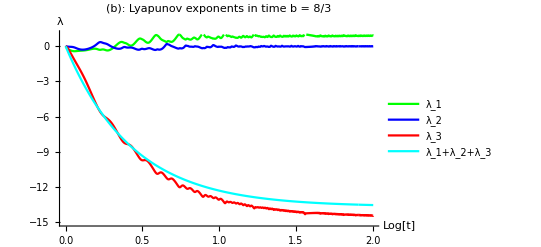

```mathematica
Show[p1,p2,p3,p4,PlotRange->{{0,2},{-15,1}}, PlotLabel->"(b): Lyapunov exponents in time b = 8/3", AxesOrigin->Automatic,AxesLabel->{"Log[t]","λ"}]
```

As is clear from the plot, the values have converged. One can also see that the sum of the exponents shows almost no oscillations over time compared to the individual exponents. This confirms that the sum is indeed numerically more stable.